Conjuntos de datos

Muchas veces, las actividades relacionadas con la computación están orientadas al manejo de grandes volúmenes de información estructurada, particularmente, en las organizaciones de gran tamaño. Wolfram Language cuenta con una forma muy eficaz de manejar información estructurada, mediante lo que se llama conjuntos de datos.

Un ejemplo simple de conjunto de datos se forma a partir de una asociación de asociaciones.

Cree un conjunto de datos simple, que contenga 2 filas y 3 columnas:

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

Dataset[<>]

Casi siempre, Wolfram Language muestra los conjuntos de datos en forma tabular. Se pueden extraer partes de un conjunto de datos de la misma manera que se haría con una asociación.

Extraiga el elemento en la “fila b” y la “columna z”:

```mathematica
data["b","z"]
```

7

O podría extraerse primero la “fila b” completa y, de ahí, extraer el elemento “z”:

```mathematica
data["b"]["z"]
```

7

También podría extraerse la “fila b” completa del conjunto de datos. El resultado es un nuevo conjunto de datos, que en este caso se muestra en forma de columna para facilitar su lectura.

Genere un nuevo conjunto de datos a partir de la “fila b” del conjunto de datos original:

```mathematica
data["b"]
```

Dataset[<>]

Aquí se muestra el conjunto de datos correspondiente a la “columna z” para todos las “filas”.

Genere un conjunto de datos que conste de la “columna z” para todas las filas:

```mathematica
data[All,"z"]
```

Dataset[<>]

La extracción de partes de un conjunto de datos es apenas el comienzo. Dondequiera que se pueda extraer una parte, puede pensarse en una función que se aplique a todas las partes en ese nivel.

Obtenga los totales de cada fila aplicando Total a todas las columnas en cada una de las filas:

```mathematica
data[All,Total]
```

Dataset[<>]

Si se usara f en vez de Total, puede verse de inmediato lo que sucede: dicha función se está aplicando a cada una de las asociaciones “fila”.

Aplique la función f a cada fila:

```mathematica
data[All,f]
```

Dataset[<>]

Aplique una función que efectúe la suma de los elementos x y z que estén en cada una de las asociaciones:

```mathematica
data[All,#x+#z&]
```

Dataset[<>]

Puede usarse cualquier función; aquí se usará PieChart:

```mathematica
data[All,PieChart]
```

Dataset[<>]

Puede también pensarse en una función que se aplique a todos las filas.

Aquí se extrae el valor de cada “columna z” y, luego, se aplica f a la asociación de los resultados:

```mathematica
data[f,"z"]
```

f[<|a→3,b→7|>]

Se aplica f a los totales de cada una de las columnas:

```mathematica
data[f,Total]
```

f[<|a→6,b→22|>]

Encuentre el mayor de esos totales:

```mathematica
data[Max,Total]
```

22

Siempre se pueden “encadenar” consultas: por ejemplo, se encuentran primero los totales para cada fila, y luego se elige el resultado de la “fila b”.

Encuentre los totales para cada fila, y luego elegir el total de la “fila b”:

```mathematica
data[All,Total]["b"]
```

22

Lo anterior es equivalente a:

```mathematica
data["b",Total]
```

22

Especialmente cuando se trata de grandes conjuntos de datos, es usual que se quiera escoger partes de acuerdo con algún criterio. La forma de operador para Select facilita notablemente este propósito.

Escoja los números mayores que 5 de una lista:

```mathematica
Select[{1,3,6,8,2,5,9,7},#>5&]
```

{6,8,9,7}

Ahora se muestra una forma diferente de hacer lo mismo, usando Select en su forma de operador:

```mathematica
Select[#>5&][{1,3,6,8,2,5,9,7}]
```

{6,8,9,7}

La forma de operador de Select es una función que puede aplicarse para ejecutar efectivamente la operación de Select.

Forme un conjunto de datos seleccionando únicamente las filas cuya “columna z” sea mayor que 5:

```mathematica
data[Select[#z>5&]]
```

Dataset[<>]

Para cada fila, seleccione las columnas cuyos valores sean mayores que 5, lo que dejará una estructura irregular:

```mathematica
data[All,Select[#>5&]]
```

Dataset[<>]

Normal convierte el conjunto de datos en una asociación común y corriente de asociaciones:

```mathematica
Normal[%]
```

<|a→<||>,b→<|y→10,z→7|>|>

Muchas de las funciones de Wolfram Language admiten formas de operador.

Ordene de acuerdo con los valores de alguna función aplicada a cada elemento:

```mathematica
SortBy[{1,3,6,8,2,5,9,7},If[EvenQ[#],#,10+#]&]
```

{2,6,8,1,3,5,7,9}

SortBy tiene una forma de operador:

```mathematica
SortBy[If[EvenQ[#],#,10+#]&][{1,3,6,8,2,5,9,7}]
```

{2,6,8,1,3,5,7,9}

Ordene las filas de acuerdo con el valor de la diferencia entre las columnas x e y:

```mathematica
data[SortBy[#x-#y&]]
```

Dataset[<>]

Ordene las filas y, luego, encuentre el total de cada columna:

```mathematica
data[SortBy[#x-#y&],Total]
```

Dataset[<>]

En ocasiones, se desea aplicar alguna función a cada uno de los elementos del conjunto de datos.

Aplique f a cada uno de los elementos del conjunto de datos:

```mathematica
data[All,All,f]
```

Dataset[<>]

Ordene las filas antes de totalizar los cuadrados de sus elementos :

```mathematica
data[SortBy[#x-#y&],Total,#^2&]
```

Dataset[<>]

Los conjuntos de datos pueden contener mezclas arbitrarias de listas y asociaciones. Aquí se ve uno, que puede verse como si fuera una lista de registros con campos denominados.

Un conjunto de datos formado a partir de una lista de asociaciones:

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

Dataset[<>]

No hay problema si faltan algunas entradas:

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7|>}]
```

Dataset[<>]

Después de estos sencillos ejemplos, puede pasarse a algo ligeramente más realista. Se importa un conjunto de datos que contiene propiedades de planetas y lunas. El conjunto de datos tiene una estructura jerárquica, donde cada planeta tiene una masa y un radio propios, así como también una colección de lunas, cada una de las cuales tiene, a su vez, sus propiedades particulares. En la práctica es muy común esta estructura general (ej., alumnos y calificaciones, clientes y pedidos, etc.).

Se trae de la nube un conjunto de datos jerárquico, sobre planetas y lunas:

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

Dataset[<>]

Obtenga el radio de cada uno de los planetas:

```mathematica
planets[All,"Radius"]
```

Dataset[<>]

Haga un diagrama de barras con los radios de los planetas:

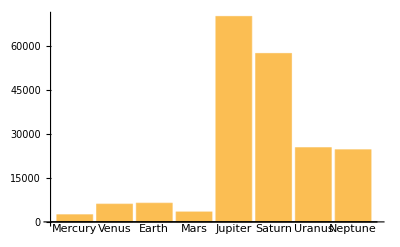

```mathematica
BarChart[planets[All,"Radius"],ChartLabels->Automatic]
```

Si se piden las lunas de Marte se obtiene un conjunto de datos, al que se pueden hacer consultas ulteriores.

Obtenga un conjunto de datos de las lunas de Marte:

```mathematica
planets["Mars","Moons"]
```

Dataset[<>]

Se “escarba más” para hacer una tabla con los radios de las lunas de Marte:

```mathematica
planets["Mars","Moons",All,"Radius"]
```

Dataset[<>]

Se pueden efectuar cómputos relativos a las lunas de todos los planetas. Para empezar, se ve cuántas lunas aparecen en la lista para cada planeta.

Haga un conjunto de datos para el número de lunas listadas para cada planeta:

```mathematica
planets[All,"Moons",Length]
```

Dataset[<>]

Obtenga la masa total de todas las lunas de cada planeta:

```mathematica
planets[All,"Moons",Total,"Mass"]
```

Dataset[<>]

Obtenga el mismo resultado, pero solamente para aquellos planetas con más de 10 lunas:

```mathematica
planets[Select[Length[#Moons]>10&],"Moons",Total,"Mass"]
```

Dataset[<>]

Haga el diagrama circular del resultado anterior:

```mathematica
PieChart[%,ChartLegends->Automatic]
```

-Graphics-

Haga un conjunto de datos con las lunas que tengan más del 1% de la masa de la Tierra.

Para cada una de las lunas, seleccione aquellas cuya masa sea mayor que 0.01 veces la masa de la Tierra:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]]
```

Dataset[<>]

Obtenga la lista de claves (esto es, los nombres de las lunas) en la asociación que resulta para cada planeta:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][All,Keys]
```

Dataset[<>]

Obtenga la asociación subyacente:

```mathematica
Normal[%]
```

<|Mercury→{},Venus→{},Earth→{Moon},Mars→{},Jupiter→{Callisto,Ganymede,Io},Saturn→{Titan},Uranus→{},Neptune→{}|>

Junte, o “concatene”, las listas para todas las claves:

```mathematica
Catenate[%]
```

{Moon,Callisto,Ganymede,Io,Titan}

Aquí aparece, en una sola fila, el cómputo completo:

```mathematica
planets[All,"Moons",Select[#Mass>LinguisticAssistant&]][Catenate,Keys]//Normal
```

{Moon,Callisto,Ganymede,Io,Titan}

Un ejemplo más: se encuentra el logaritmo de la masa de cada luna y se hace, para cada planeta, una gráfica de recta numérica para dichos valores.

Haga las gráficas de recta numérica para los logaritmos de las masas de las lunas de cada planeta:

```mathematica
planets[All,"Moons",NumberLinePlot[Values[#]]&,Log[#Mass/LinguisticAssistant]&]
```

Dataset[<>]

Como otro ejemplo, se hace la nube de palabras con los nombres de las lunas, con los tamaños dependiendo de las masas respectivas. Para este fin, se requiere una sola asociación que asocie el nombre de cada luna con su masa.

Cuando se da una asociación, WordCloud determina los tamaños de acuerdo con los valores en la asociación:

```mathematica
WordCloud[<|"A"->5,"B"->4,"C"->3,"D"->2,"E"->1|>]
```

-Graphics-

La función Association combina asociaciones:

```mathematica
Association[<|"a"->1,"b"->2|>,<|"c"->3|>]
```

<|a→1,b→2,c→3|>

Genere la nube de palabras de las masas de las lunas:

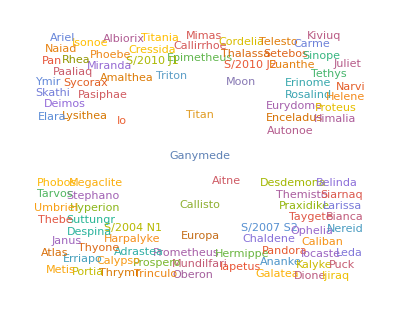

```mathematica
planets[WordCloud[Association[Values[#]]]&,"Moons",All,"Mass"]
```

Considerando todo lo que hace, el código usado es sorprendentemente sencillo. Puede mejorarse aún más si se usa @* o /*.

Se vio anteriormente que es posible escribir algo tipo f[g[x]] como f@g@x o x//g//f. Puede también escribirse f[g[#]]&[x]. Pero, ¿y qué hay con f[g[#]]&? ¿Hay alguna forma abreviada de escribirlo? Sí, la hay, en términos de los operadores de composición de funciones @* y /*.

f@*g@*h representa una composición de funciones que se aplica de derecha-a-izquierda:

```mathematica
(f@*g@*h)[x]
```

f[g[h[x]]]

h/*g/*f representa una composición de funciones que se aplican de izquierda-a-derecha:

```mathematica
(h/*g/*f)[x]
```

f[g[h[x]]]

Aquí se presenta el código anterior reescrito en términos de la composición @*:

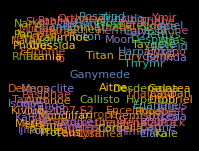

```mathematica
planets[WordCloud@*Association@*Values,"Moons",All,"Mass"]
```

O bien, usando la composición por la derecha /*:

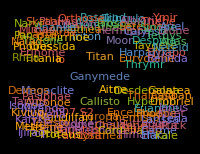

```mathematica
planets[Values/*Association/*WordCloud,"Moons",All,"Mass"]
```

Como último ejemplo, se considera otro conjunto de datos, que ahora procede directamente del Wolfram Data Repository. Aquí aparece una página web (sobre meteoros grandes) del repositorio:

-Graphics-

Para traer el conjunto de datos principal que se menciona aquí, se usa simplemente ResourceData.

Obtenga el conjunto de datos, simplemente dando su nombre a ResourceData:

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

Dataset[<>]

Extraiga el campo de las coordenadas de cada fila, y grafique los resultados:

```mathematica
GeoListPlot[fireballs[All,"Coordinates"]]
```

-Graphics-

Haga un histograma de las altitudes:

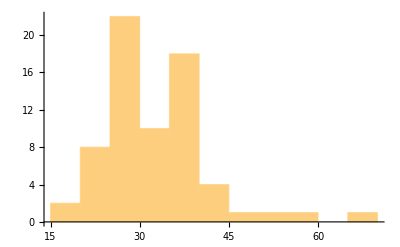

```mathematica
Histogram[fireballs[All,"Altitude"]]
```

Vocabulario

Dataset[data] |   | un conjunto de datos
Normal[dataset] |   | convierte un conjunto de datos en listas y asociaciones normales
Catenate[{assoc_1, ...}] |   | concatena asociaciones, combinando sus elementos
f@*g |   | composición de funciones (f[g[x]] al aplicarla a x)
f/*g |   | composición por la derecha (g[f[x]] al aplicarla a x)

"13 Exercises Available" | "Get Started »"

Nota: Estos ejercicios usan el conjunto de datos planets=CloudGet["http: // wolfr.am/7FxLgPm5"].

Haga una nube de palabras de los planetas, con los pesos determinados por el número de lunas que tienen. »

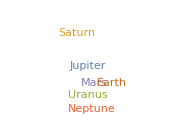
| Expected output: |  
  | -Graphics- |

Haga un diagrama de barras del número de lunas de cada .08planeta. »

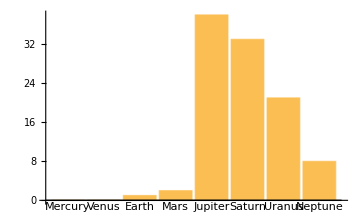
| Expected output: |  
  | -Graphics- |

Construya un conjunto de datos con las masas de los planetas, ordenados por el número de sus lunas. »

| Expected output: |  
  | Dataset[<>] |

Forme un conjunto de datos de cada planeta y la masa de su luna más masiva. »

| Expected output: |  
  | Dataset[<>] |

Genere un conjunto de datos con las masas de los planetas, ordenados de acuerdo con la masa de la mayor de sus lunas. »

| Expected output: |  
  | Dataset[<>] |

Forme un conjunto de datos con las medianas de las masas de las lunas de cada planeta. »

| Expected output: |  
  | Dataset[<>] |

Para cada uno de los planetas, construya una lista de las lunas cuyas masas sean mayores que 0.0001 veces la masa de la Tierra. »

| Expected output: |  
  | Dataset[<>] |

Haga una nube de palabras de los países centroamericanos, con los nombres proporcionales a las longitudes de sus respectivos artículos en Wikipedia. »

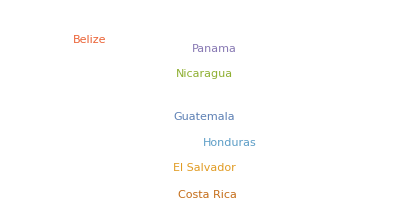
| Sample expected output: |  
  | -Graphics- |

Encuentre la altitud máxima observada en el conjunto de datos Fireballs & Bolides. »

| Expected output: |  
  | 66.6 "km" |

Encuentre el conjunto de datos de las 5 mayores altitudes observadas en el conjunto de datos Fireballs & Bolides. »

| Expected output: |  
  | Dataset[<>] |

Haga un histograma con las diferencias entre tiempos sucesivos del brillo pico en el conjunto de datos Fireballs & Bolides. »

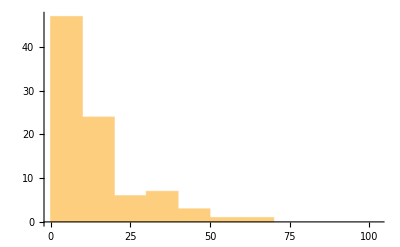
| Expected output: |  
  | -Graphics- |

Grafique las ciudades más próximas para los 10 primeros casos en el conjunto de datos Fireballs & Bolides, con etiquetas para cada ciudad. »

| Expected output: |  
  | -Graphics- |

Presente gráficamente las ciudades más próximas para los 10 casos con mayores altitudes en el conjunto de datos Fireballs & Bolides, con etiquetas para cada ciudad. »

| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué tipo de información pueden contener los conjuntos de datos?

Cualquier tipo. No solo números y texto, sino también imágenes, gráficos, y muchas otras cosas. Además, no es necesario que todos los elementos de una fila o columna dada sean del mismo tipo.

¿Se pueden convertir hojas de cálculo a conjuntos de datos?

Sí. Y una buena forma de hacerlo es con SemanticImport.

¿Qué son las bases de datos y cómo se relacionan con Dataset?

Las bases de datos son la forma tradicional de guardar información estructurada en un sistema de cómputo y, por lo general, están diseñadas para permitir tanto la lectura como la escritura de información. Dataset es una forma de representar la información guardada en una base de datos de modo tal que pueda manipularse con Wolfram Language.

¿Cómo se compara la información en Dataset con la existente en una base de datos SQL relacional?

Las bases de datos SQL se basan estrictamente en tablas de datos acomodados en filas y columnas de tipos determinados, con datos adicionales vinculados mediante”claves externas”. Dataset puede tener una mezcla cualquiera de tipos de información, con cualquier número de niveles de anidación y cualquier estructura jerárquica, que tiene un poco más de analogía con una base de datos NoSQL, pero con operaciones adicionales que se posibilitan debido a la naturaleza simbólica del lenguaje.

¿Pueden usarse conjuntos de datos para armar entidades y valores asociados con ellas?

Sí. Si se tiene un conjunto de datos que sea una asociación de asociaciones, cuyas claves exteriores sean entidades y cuyas interiores sean propiedades, entonces es suficiente con poner esto dentro de EntityStore, y con esto se tiene prácticamente todo armado.

Notas técnicas

Dataset maneja un nuevo tipo de estructura simbólica de base de datos, que generaliza tanto las bases de datos relacionales como las jerárquicas.

Dataset tiene muchos otros mecanismos y capacidades adicionales que no se vieron en esta sección.

Todo lo que pueda hacerse con consultas a conjuntos de datos puede hacerse también usando funciones tales como Map y Apply en las listas y asociación subyacentes; pero, por lo general, es más simple hacerlo mediante consultas al conjunto de datos.

Wolfram Language puede conectarse directamente con bases de datos SQL, y hacer consultas con la sintaxis de SQL, usando DatabaseLink.

Para explorar más

Guía para computación con conjuntos de datos estructurados en Wolfram Language »